```mathematica
Func20[x_]:=Module[{R1,R2},
R1 = Sin[(√13 x^3-9x-5-√17)/10];
R2 = Tan[(x^2+x+2^(1/3))/(3x-5)];
Return [R1 + R2 + 0.6]
];
Func23[x_]:=Module[{R1,R2},
R1 = Sin[(-2 x^2-√10 x+1)/4];
R2 = ((x^2+(√2+R1)*x - 3)/(R1*x - 3))^Log[2];
Return [R1 + R2 -1.2]
];
pointsgrid[a_,b_,i_,n_]:=a + (i-1) * (b-a)/(n-1);
ii[x_]:=x;
xx[x_]:=x^2;
```

```mathematica
SetDirectory[NotebookDirectory[]];
f = Func20;
var = "20";
namex=StringJoin["output/vecx",var,".dat"];
namey = StringJoin["output/vecy",var,".dat"];
nameintery= StringJoin["output/vecintery",var,".dat"];
x =Flatten@ Import[namex];
y =Flatten@  Import[namey];
intery =Flatten@  Import[nameintery];
points=Table[{x⟦i⟧,y⟦i⟧},{i,1,Length@x}];
interpoints = Table[{pointsgrid[x⟦1⟧,x⟦-1⟧,i,Length@intery],intery⟦i⟧},{i,1,Length@intery}];
```

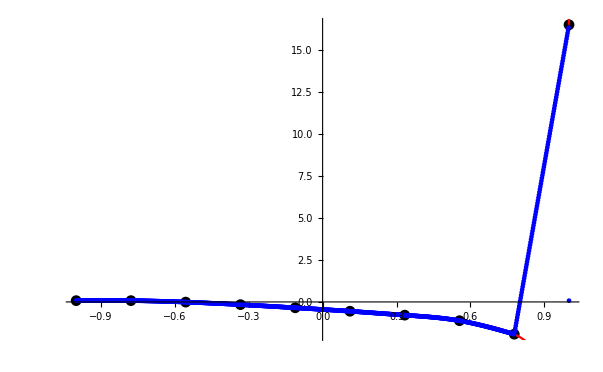

```mathematica
Discret= ListPlot[points,PlotRange->All,PlotStyle->{Black}];
Reall = Plot[f[x],{x,-1,1},PlotStyle->{Red},PlotRange->All];
Inter=ListPlot[interpoints,PlotRange->All,PlotStyle->{Blue}];
Show[Discret,Reall,Inter]
```